```mathematica
p=6
g[x_]:=((Cos[2 π/p]) x-Sin[2 π/p])/((Sin[2 π/p]) x+Cos[2 π/p]);
Nest[g,x,p]//FullSimplify
```

6

x

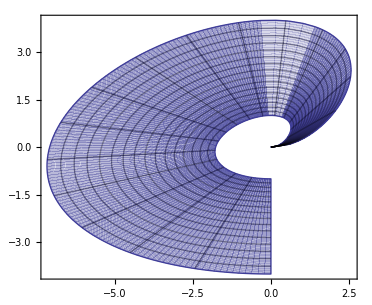

```mathematica
ParametricPlot[r^2{ Sqrt[t]Cos[t], Sin[t]},{t,0,3Pi/2},{r,1,2},PlotPoints->50]
```

```mathematica
Export["F:\\pic\\math\\3.jpg",Image[%,ImageSize->{1600,960}]]
```

F:\pic\math\3.jpg

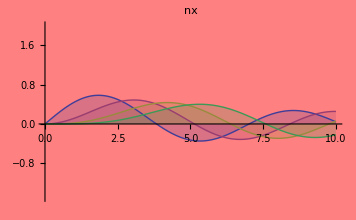

F:\pic\math\2.jpg

```mathematica
Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Background->RGBColor[Random[],Random[],Random[]],PlotPoints->5000,PlotStyle->Thick,Filling->Axis,PlotLabel->BesselJ[n,x],PlotRange->{{0,10},{-1.5,2}}]
Export["F:\\pic\\math\\2.jpg",Image[%,ImageSize->{1600,960}]]
```

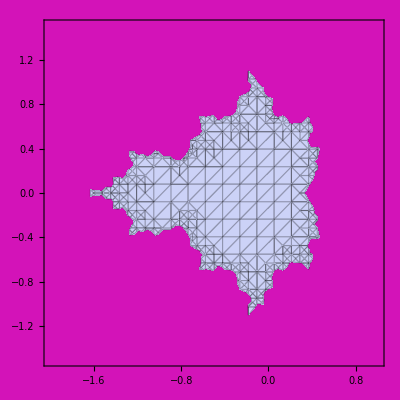

```mathematica
RegionPlot[Abs[Nest[(#^2+x+I y)&,x+I y,8]]<2,{x,-2,1},{y,-1.5,1.5},Mesh->All,Background->RGBColor[Random[],Random[],Random[]]]
```

```mathematica
Export["F:\\pic\\math\\15.jpg",Image[%,ImageSize->{1600,960}]]
```

F:\pic\math\15.jpg